# Erzwungene Schwingungen

## Aufgabe 1

## ohne Dämpfung

```mathematica
A1 =  {9, 8.8, 8.7, 8.5, 8.4, 8.2, 8.1, 8, 7.8, 7.7, 7.6, 7.4, 7.3, 7.2, 7, 6.9, 6.7, 6.6, 6.5, 6.3, 6.2, 6.1, 5.9, 5.8, 5.7, 5.5, 5.4, 5.3, 5.1, 5};
```

```mathematica
A2 = {9, 8.9, 8.7, 8.5, 8.4, 8.3, 8.1, 7.9, 7.8, 7.6, 7.5, 7.3, 7.2, 7, 6.9, 6.7, 6.6, 6.5, 6.4, 6.2, 6.1, 5.9, 5.8, 5.7, 5.5, 5.4, 5.3, 5.2, 5, 4.8};
```

```mathematica
Length[A1]
```

30

```mathematica
Length[A2]
```

30

Frequenz = 20 s für 10 Perioden

gemessen durch Simon

## mit Dämpfung 0.45 A

```mathematica
A3 = {9,7.1,5.7,4.5,3.5,2.7,2.2,1.7,1.4,1};
```

```mathematica
A4 = {9,7.2,5.8,4.5,3.5,2.7,2.1,1.6,1.2,0.9};
```

```mathematica
Length[A3]
```

10

```mathematica
Length[A4]
```

10

Frequenz 20 = s für 10 Periode
A3 gemessen durch batritschia
A4 gemessen durch Simon

## mit Dämpfung 0.6 A

```mathematica
A5 = {9,6,4,2.6,1.7,1.1,0.6,0.4,0.2,0.1};
A6 = {9,6,4,2.7,1.8,1.2,0.7,0.4,0.3,0.1};
```

```mathematica
Length[A5] == Length[A6]
```

True

```mathematica
f6 = 1/(20/10);
```

Periode = 20 s für 10 Perioden

patritschia liest werte ab und simon misst die zeit;

## Aufgabe 2

## mit 0.6 A

```mathematica
A7 = Table[(A5[[i]] + A6[[i]])/2, {i, 1, 10}];
```

resonanzfreq

```mathematica
alpha6 = -f6*Log[A7[[10]]/A7[[1]]]/9
```

0.249989

```mathematica
omega6 = Sqrt[(2π*f6)^2-2alpha6^2] / 2/π
```

0.496824

```mathematica
1/omega6
```

2.01279

```mathematica
A8 = {{22, 1.3},{20,2.1},{18,1.05},{16,0.45},{21,1.9},{21.5,1.7},{19,1.4},{20.5,2.15}};
```

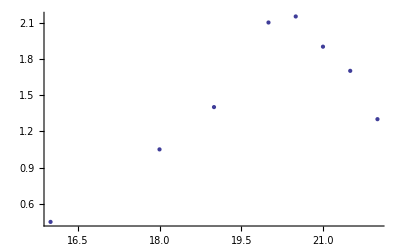

```mathematica
ListPlot[A8]
```

## mit 0.45 A

```mathematica
A9 = Table[(A3[[i]] + A4[[i]])/2, {i, 1, 10}];
```

```mathematica
alpha45 = -f6*Log[A9[[10]]/A9[[1]]]/9
```

0.124918

```mathematica
omega45 = Sqrt[(2π*f6)^2-2alpha45^2] / 2/π
```

0.499209

```mathematica
1/omega45
```

2.00317

```mathematica
A10 = {{20.5, 3.45},{19,1.5},{19.5,2.9},{20,3.55},{20.2,3.6},{18.2,1.25},{19.1,2.5}};
```

```mathematica
3.6/Sqrt[2]
```

2.54558

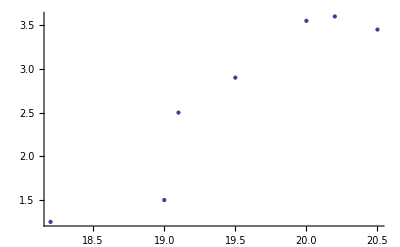

```mathematica
ListPlot[A10]
```

## ohne

```mathematica
A11 = Table[(A1[[i]] + A2[[i]])/2, {i, 1, 10}];
```

```mathematica
alpha0 = -f6*Log[A11[[10]]/A11[[1]]]/9
```

0.00902883

```mathematica
omega0 = Sqrt[(2π*f6)^2-2alpha0^2] / 2/π
```

0.499996

```mathematica
1/omega0
```

2.00002

```mathematica
A12 = {{19.1,4.1},{20,8.6},{20.5,4.3},{22.0,1.7},{21,2.9},{18.5,1.5},{19.5,6}};
```

```mathematica
3.6/Sqrt[2]
```

2.54558

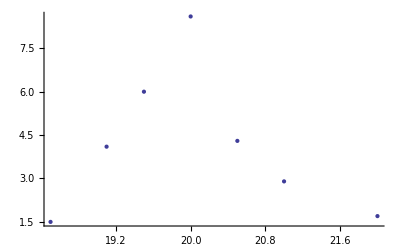

```mathematica
ListPlot[A12]
```